```mathematica
Fulls=Association[]
```

<||>

```mathematica
Table[Fulls[k]=Association[],{k,Keys[allGraphs5]}];
```

```mathematica
Monitor[Table[Fulls[k,"graph"]=EmbedGraphInPlantri8[allGraphs5,k],{k,Keys[allGraphs5]}],k];
```

```mathematica
Monitor[Table[Fulls[k,"chromial"]=ChromaticPolynomial[Fulls[k,"graph"],x],{k,Keys[allGraphs5]}],k];
```

```mathematica
FindFullFormula
```

FindFullFormula

```mathematica
Monitor[Table[Fulls[k,"colofour"]=FindFullFormula[Fulls[k,"graph"]],{k,allGraphs5AtomKeys}],k]
```

```mathematica
Table[{k,Fulls[k,"chromial"]/.x->4},{k,allGraphs5AtomKeys}]
```

{{29524,0},{29525,240},{29527,144},{29533,480},{29537,336},{29551,264},{29560,744},{29605,144},{29608,0},{29633,240},{29767,240},{29768,336},{29797,240},{29857,336},{29888,264},{30253,264},{30262,696},{30334,192},{30496,384},{30586,264},{31711,216},{31714,72},{31738,192},{31954,192},{31984,96},{32441,480},{32684,288},{36085,216},{36086,192},{36112,192},{36166,72},{36194,96},{36817,312},{36898,120},{38281,168},{38308,216},{39014,384},{49207,264},{49208,384},{49210,192},{49216,696},{49220,264},{49963,504},{49972,624},{51475,312},{51478,120},{52232,432},{56011,480},{56012,288},{56770,432},{58288,384},{59048,384}}

```mathematica
Table[{k,Fulls[k,"chromial"]/.x->4},{k,allGraphs5AtomKeys}]
```

```mathematica
Table[ShowGraph[allGraphs5,k],{k,Select[allGraphs5AtomKeys,(Fulls[#,"chromial"]/.x->4)==0&]}]
```

{-Graphics-29524,-Graphics-29608}

```mathematica
Fulls[29608,"chromial"]//Factor
```

(-4+x) (-3+x) (-2+x) (-1+x) x (-124884+258889 x-246724 x^2+142716 x^3-55448 x^4+15036 x^5-2846 x^6+362 x^7-28 x^8+x^9)

```mathematica
Select[Keys[allGraphs5],(Fulls[#,"chromial"]/.x->4)==0&]
```

{29524,29608}

```mathematica
Graph[Fulls[29608,"graph"],GraphLayout->"LayeredDigraphEmbedding",VertexLabels->"Name"]
```

```mathematica
full29608=FindFullFormula[Fulls[29608,"graph"]]
```

{v1x2x3x4x5x6x7x8x9xaxbxcxdxg,v1x2x3x4x5x6x7x8x9xaxbxcgxd,v1x2x3x4x5x6x7x8x9xaxbdxcxg,v1x2x3x4x5x6x7x8x9xaxbdxcg,v1x2x3x4x5x6x7ax8x9xbxcxdxg,v1x2x3x4x5x6x7ax8x9xbxcgxd,v1x2x3x4x5x6x7ax8x9xbdxcxg,v1x2x3x4x5x6x7ax8x9xbdxcg,v1x2x3x4x5x6x7x8x9xadxbxcxg,v1x2x3x4x5x6x7x8x9xadxbxcg,v1x2x3x4x5x6x7x8x9xacxbxdxg,v1x2x3x4x5x6x7x8x9xacxbdxg,v1x2x3x4x5x6x79x8xaxbxcxdxg,v1x2x3x4x5x6x79x8xaxbxcgxd,v1x2x3x4x5x6x79x8xaxbdxcxg,647217,v18bx24dx35gx69x7xac,v18bx24gx35x69x7xacxd,v18bx24gx357x69xacxd,v18x24x35x69x7xacxbdxg,v18acx24x35x69x7xbdxg,v18x24x357x69xacxbdxg,v18acx24x357x69xbdxg,v18x24x35gx69x7xacxbd,v18acx24x35gx69x7xbd,v18x24gx35x69x7xacxbd,v18acx24gx35x69x7xbd,v18x24gx357x69xacxbd,v18acx24gx357x69xbd,v18gx24x35x69x7xacxbd,v18gx24x357x69xacxbd}
 |  |  |  |

```mathematica
Map[StringCount[SymbolName[#],"x"]&,full29608]//Tally
```

{{13,1},{12,53},{11,1080},{10,10874},{9,57997},{8,163709},{7,231967},{6,146892},{5,33088},{4,1586}}

```mathematica
Table[ShowGraph[allGraphs5,k],{k,Select[allGraphs5AtomKeys,IsomorphicGraphQ[allGraphs5[#,"graph"],CompleteGraph[4]]&]}]
```

{-Graphics-29525,-Graphics-29527,-Graphics-29533,-Graphics-29551,-Graphics-29605,-Graphics-29767,-Graphics-30253,-Graphics-31711,-Graphics-36085,-Graphics-49207}

```mathematica
29527
```

```mathematica
full29527=FindFullFormula[Fulls[29527,"graph"]]
```

{v1x2x3x4x5x6x7x8x9xaxbxcxdxfxg,v1x2x3x4x5x6x7x8x9xaxbxcxdgxf,v1x2x3x4x5x6x7x8x9xaxbxcgxdxf,v1x2x3x4x5x6x7x8x9xaxbfxcxdxg,v1x2x3x4x5x6x7x8x9xaxbfxcxdg,v1x2x3x4x5x6x7x8x9xaxbfxcgxd,v1x2x3x4x5x6x7x8x9xaxbdxcxfxg,v1x2x3x4x5x6x7x8x9xaxbdxcgxf,v1x2x3x4x5x6x7ax8x9xbxcxdxfxg,v1x2x3x4x5x6x7ax8x9xbxcxdgxf,v1x2x3x4x5x6x7ax8x9xbxcgxdxf,v1x2x3x4x5x6x7ax8x9xbfxcxdxg,v1x2x3x4x5x6x7ax8x9xbfxcxdg,v1x2x3x4x5x6x7ax8x9xbfxcgxd,3992408,v18bdx24gx35fx69x7xac,v18acx24gx35fx69x7xbd,v18gx24x35fx69x7xacxbd,v18x24fx35x69x7xacxbdxg,v18bdx24fx35x69x7xacxg,v18acx24fx35x69x7xbdxg,v18x24fx357x69xacxbdxg,v18bdx24fx357x69xacxg,v18acx24fx357x69xbdxg,v18x24fx35gx69x7xacxbd,v18bdx24fx35gx69x7xac,v18acx24fx35gx69x7xbd,v18gx24fx35x69x7xacxbd,v18gx24fx357x69xacxbd}
 |  |  |  |

```mathematica
Map[StringCount[SymbolName[#],"x"]&,full29527]//Tally
```

{{14,1},{13,64},{12,1610},{11,20593},{10,144968},{9,569580},{8,1214382},{7,1308956},{6,625157},{5,103568},{4,3551},{3,6}}

```mathematica
Table[ShowGraph[allGraphs5,k],{k,Select[Keys[allGraphs5],(Fulls[#,"chromial"]/.x->4)==0&]}]
```

{-Graphics-29524,-Graphics-29608}

```mathematica
Keys[allGraphs5]//Length
```

1895

```mathematica
Keys[Fulls[1]]
```

{graph,chromial}

```mathematica
allGraphs5[29608,"colofour"]
```

v1x24x35

```mathematica
Select[Keys[allGraphs5],Intersection[{v1x24x35},ListofVars[allGraphs5[#,"colofour"]]]≠{}&]//Length
```

328

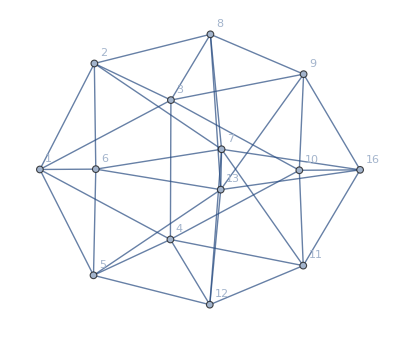

```mathematica
Graph[Fulls[29608,"graph"],VertexLabels->"Name"]
```

```mathematica
Monitor[Table[{(Fulls[k,"chromial"]/.x->4)/24,k},{k,Sort[Keys[allGraphs5]]}],k]//Sort
```

{{0,29524},{0,29608},{3,31714},{3,36166},{4,31984},{4,36194},{5,7738},{5,22318},{5,36898},{5,51478},{6,29443},{6,29446},{6,29521},{6,29527},{6,29602},{6,29605},{7,31444},{7,36138},{7,38281},{8,11950},{8,30334},{8,31738},{8,31954},{8,35434},{8,36086},{8,36112},{8,49210},{9,22963},{9,23041},{9,23044},{9,27259},{9,27337},{9,27340},{9,31711},{9,36085},{9,38308},1823,{307,2269},{307,6807},{309,244},{312,2271},{312,6645},{314,2214},{314,6588},{316,732},{316,19764},{328,2430},{328,6562},{342,30},{342,108},{354,2188},{354,6804},{355,82},{355,246},{364,4},{364,324},{364,8748},{368,9},{368,2190},{368,6642},{385,84},{388,729},{388,19683},{392,2268},{392,6564},{423,27},{436,1},{436,243},{464,2187},{464,6561},{488,3},{488,81},{628,0}}
 |  |  |  |

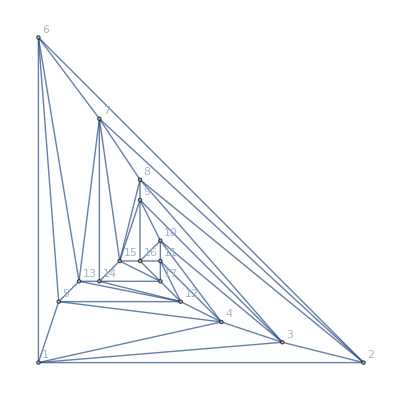

```mathematica
Graph[plantri[[8]],GraphLayout->"PlanarEmbedding",VertexLabels->"Name"]
```

```mathematica
EmbedGraphInPlantri8[assoc_,key_]:=Block[{val=assoc[key], sets, reference={12,13,7,15,17}, g, sub},
sets=val["vertexsets"];
g=VertexDelete[ Graph[plantri[[8]]],14];
g=EdgeDelete[ g,{7<->13,13<->12,12<->17,17<->15,15<->7}];
Table[If[Length[s]>1,
g=VertexContract[g,Table[reference[[v]],{v,s}]]
], {s,sets}];
sub=val["graph"];
Table[
g=EdgeAdd[g,{reference[[First[sets[[e[[1]]]]]]]<->reference[[First[sets[[e[[2]]]]]]]}],{e,EdgeList[sub]}];

g
]
```